# Versuch 49

```mathematica
ClearAll["Global`*"]
```

## Einstellungen

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15]}
```

{Frame→True,Axes→False,FrameStyle→Directive[GrayLevel[0],Thickness[0.003]],ImageSize→700,FrameTicksStyle→Directive[GrayLevel[0],15]}

```mathematica
legendSettings={LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}};
```

## Fehlerrechnung

```mathematica
errorVolt[reading_,range_]:=If[range==1,0.025reading+0.006range,If[range==10,0.025reading+0.005range,If[range==100,0.025reading+0.005range,If[range==100,0.025reading+0.005range]]]]
```

```mathematica
errorCurrent[reading_,range_]:=If[range==10,0.05reading+0.015range,If[range==100,0.05reading+0.005range]]
```

## Gaussgewichtete Regression

```mathematica
gaussReg[xdata_,ydata_,dydata_]:=With[{Δ=Total[1/#^2&/@ dydata]Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[xdata]}])^2},{1/Δ(Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}] Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), 1/Δ(Total[1/#^2&/@ dydata]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), Sqrt[1/Δ Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]], Sqrt[1/Δ Total[1/#^2&/@ dydata]]} ]
```

## Schottky-Langmuir-Raumladungsgesetz

```mathematica
rawData65=Import[NotebookDirectory[]<>"Anodenstrom Uh 6.5 V.xlsx"][[1]];
```

```mathematica
data65=SortBy[rawData65[[All,1;;2]],First];
```

```mathematica
rawData65
```

{{10.594,0.16,10.,10.},{19.82,0.3435,100.,10.},{31.074,0.6278,100.,10.},{40.024,0.8728,100.,10.},{50.02,1.157,100.,10.},{59.594,1.412,100.,10.},{70.523,1.696,100.,10.},{80.257,1.94,100.,10.},{90.42,2.1437,100.,10.},{100.601,2.356,100.,10.},{110.914,2.5372,100.,10.},{120.15,2.65,1000.,10.},{130.21,2.72,1000.,10.},{139.63,2.7731,1000.,10.},{150.31,2.7975,1000.,10.},{160.55,2.8262,1000.,10.},{169.5,2.727,1000.,10.},{180.36,2.88,1000.,10.},{190.57,2.7835,1000.,10.},{200.2,2.8795,1000.,10.},{210.45,2.853,1000.,10.},{219.5,2.876,1000.,10.},{230.01,2.913,1000.,10.},{239.89,2.854,1000.,10.},{250.53,2.872,1000.,10.},{260.18,2.826,1000.,10.},{270.12,2.8862,1000.,10.},{280.3,2.92,1000.,10.},{290.99,2.9176,1000.,10.},{300.14,2.9392,1000.,10.},{310.33,2.9263,1000.,10.},{320.84,2.93,1000.,10.},{330.41,2.9155,1000.,10.},{340.58,2.9305,1000.,10.},{350.99,2.8352,1000.,10.},{360.76,2.841,1000.,10.},{370.8,3.1064,1000.,10.},{380.31,3.0875,1000.,10.},{390.65,3.1153,1000.,10.},{400.56,3.0529,1000.,10.},{410.96,2.9875,1000.,10.},{420.59,3.0875,1000.,10.},{429.99,3.0524,1000.,10.},{440.39,3.0025,1000.,10.},{450.65,3.0383,1000.,10.},{460.99,3.1253,1000.,10.},{470.87,3.1666,1000.,10.},{480.72,3.1597,1000.,10.},{490.15,2.9853,1000.,10.},{500.02,3.0165,1000.,10.},{15.037,0.2403,100.,10.},{25.555,0.4683,100.,10.},{-500.,-0.0003,1000.,10.},{-400.75,-0.0003,1000.,10.},{-300.61,-0.0003,1000.,10.},{-200.01,-0.0002,1000.,10.},{-99.9,-0.0002,1000.,10.}}

```mathematica
rawData75=Import[NotebookDirectory[]<>"Anodenstrom Uh 7.5 V.xlsx"][[1]];
```

```mathematica
data75=SortBy[rawData75[[All,1;;2]],First];
```

```mathematica
yerror65=ConstantArray[0.01,Length[data65]];
yerror75=ConstantArray[0.01,Length[data75]];
```

```mathematica
xerror65=ConstantArray[0.5,Length[data65]];
xerror75=ConstantArray[0.5,Length[data75]];
```

### Abb 4

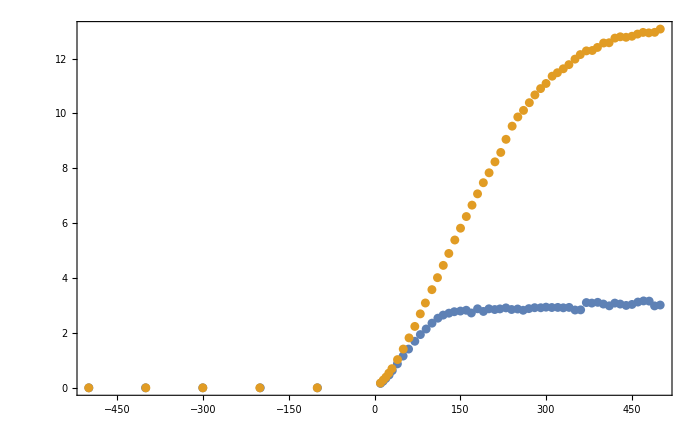

```mathematica
ListPlot[{Table[{Around[data65[[i,1]],xerror65[[i]]],Around[data65[[i,2]],yerror65[[i]]]},{i,1,Length[data65]}],Table[{Around[data75[[i,1]],xerror75[[i]]],Around[data75[[i,2]],yerror75[[i]]]},{i,1,Length[data75]}]},pltsettings,PlotRange->All]
```

### Cut The Data!!!!

```mathematica
cutData65=DeleteCases[data65,x_/;x[[1]]<0];
cutData75=DeleteCases[data75,x_/;x[[1]]<0];
```

```mathematica
cutyError65=yerror65[[-Length[cutData65];;-1]];
cutyError75=yerror75[[-Length[cutData75];;-1]];
```

```mathematica
cutxError65=xerror65[[-Length[cutData65];;-1]];
cutxError75=xerror75[[-Length[cutData75];;-1]];
```

### Abb. 5

The error in y^(2/3) is given by
Δy^(2/3)=2/3 y^(-2/3) Δy

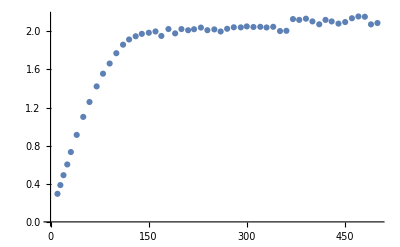

```mathematica
ListPlot[{#[[1]],#[[2]]^(2/3)}&/@cutData65]
```

```mathematica
reg1Cut=8;
```

```mathematica
pars1=gaussReg[cutData65[[1;;reg1Cut,1]],cutData65[[1;;reg1Cut,2]]^(2/3), cutyError65[[1;;reg1Cut]]]
```

{0.0948212,0.0199564,0.00774497,0.000219004}

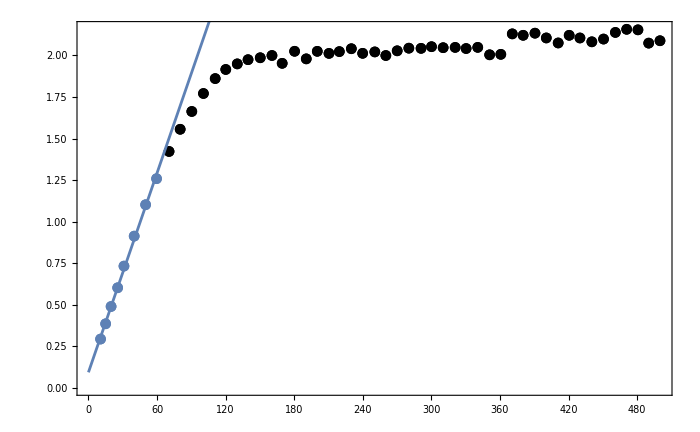

```mathematica
Show[ListPlot[Table[{{Around[cutData65⟦i,1⟧,cutxError65[[i]]],Around[cutData65⟦i,2⟧^(2/3),(2 cutyError65⟦i⟧)/(3 cutData65⟦i,2⟧^(2/3))]}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],Plot[pars1⟦1⟧+pars1⟦2⟧ x,{x,0,500}],pltsettings]
```

```mathematica
-pars1[[1]]/pars1[[2]]
```

-4.75143

### Abb. 6

The error in y^(2/3) is given by
Δy^(2/3)=2/3 y^(-2/3) Δy

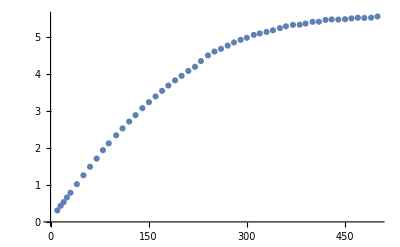

```mathematica
ListPlot[{#[[1]],#[[2]]^(2/3)}&/@cutData75]
```

```mathematica
reg2Cut=10;
```

```mathematica
pars2=gaussReg[cutData75[[1;;reg2Cut,1]],cutData75[[1;;reg2Cut,2]]^(2/3), cutyError75[[1;;reg2Cut]]]
```

{0.0742216,0.0233189,0.00639198,0.000137838}

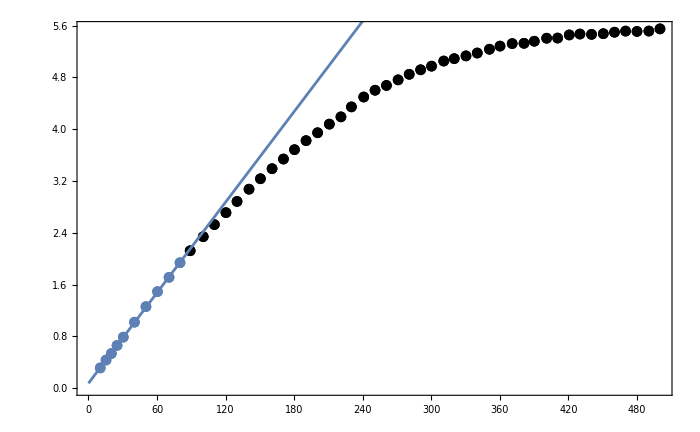

```mathematica
Show[ListPlot[Table[{{Around[cutData75⟦i,1⟧,cutxError75[[i]]],Around[cutData75⟦i,2⟧^(2/3),(2 cutyError75⟦i⟧)/(3 cutData75⟦i,2⟧^(2/3))]}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],Plot[pars2⟦1⟧+pars2⟦2⟧ x,{x,0,500}],pltsettings]
```

```mathematica
-pars2[[1]]/pars2[[2]]
```

-3.18289

### Abb 7

```mathematica
logData65=Log[cutData65]
```

{{2.36029,-1.83258},{2.71051,-1.42587},{2.98669,-1.06857},{3.24083,-0.758646},{3.43637,-0.465534},{3.68948,-0.136049},{3.91242,0.14583},{4.08755,0.345007},{4.25594,0.528273},{4.38523,0.662688},{4.50447,0.762533},{4.61116,0.856965},{4.70876,0.931061},{4.78874,0.97456},{4.86915,1.00063},{4.939,1.01997},{5.0127,1.02873},{5.07861,1.03893},{5.13285,1.0032},{5.19495,1.05779},{5.25002,1.02371},{5.29932,1.05762},{5.34925,1.04837},{5.39135,1.0564},{5.43812,1.06918},{5.48018,1.04872},{5.52358,1.05501},{5.56137,1.03886},{5.59887,1.05994},{5.63586,1.07158},{5.67329,1.07076},{5.70425,1.07814},{5.73764,1.07374},{5.77094,1.075},{5.80033,1.07004},{5.83065,1.07517},{5.86076,1.04211},{5.88821,1.04416},{5.91566,1.13346},{5.94099,1.12736},{5.96781,1.13633},{5.99286,1.11609},{6.0185,1.09444},{6.04166,1.12736},{6.06376,1.11593},{6.08766,1.09945},{6.11069,1.1113},{6.13338,1.13953},{6.15458,1.15266},{6.17528,1.15048},{6.19471,1.0937},{6.21465,1.1041}}

```mathematica
dlogx65=Table[cutxError65[[i]]/cutData65[[i,1]],{i,1,Length[cutData65]}];
dlogy65=Table[cutyError65[[i]]/cutData65[[i,2]],{i,1,Length[cutData65]}]
```

{0.0625,0.0416146,0.0291121,0.0213538,0.0159286,0.0114574,0.00864304,0.00708215,0.00589623,0.00515464,0.00466483,0.00424448,0.00394135,0.00377358,0.00367647,0.00360607,0.00357462,0.00353832,0.00366703,0.00347222,0.0035926,0.00347283,0.00350508,0.00347705,0.00343289,0.00350385,0.00348189,0.00353857,0.00346476,0.00342466,0.00342747,0.00340229,0.00341728,0.00341297,0.00342994,0.00341239,0.00352709,0.00351989,0.00321916,0.00323887,0.00320996,0.00327557,0.00334728,0.00323887,0.00327611,0.00333056,0.00329131,0.00319969,0.00315796,0.00316486,0.00334975,0.0033151}

```mathematica
pars3=gaussReg[logData65[[1;;reg1Cut,1]],logData65[[1;;reg1Cut,2]],dlogy65[[1;;reg1Cut]]]
```

{-4.86018,1.27616,0.0541735,0.0140724}

```mathematica
LinearModelFit[logData65[[1;;reg1Cut]],x,x]["RSquared"]//Sqrt//N
```

0.999659

```mathematica
cutData65[[1]]
cutData65[[-1]]
```

{10.594,0.16}

{500.02,3.0165}

```mathematica
pars3[[2]]
```

1.27616

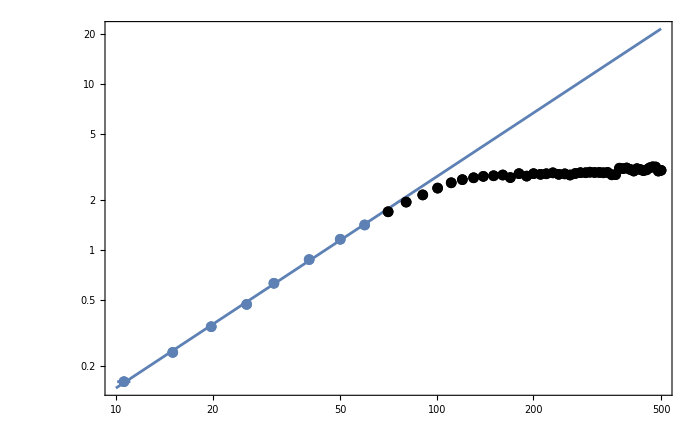

```mathematica
Show[LogLogPlot[E^pars3[[1]] x^(pars3[[2]]),{x,10,500}],ListLogLogPlot[Table[{{Around[cutData65⟦i,1⟧,cutxError65[[i]]],Around[cutData65⟦i,2⟧,cutyError65⟦i⟧]}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],pltsettings]
```

### Abb 8

```mathematica
logData75=Log[cutData75];
```

```mathematica
dlogx75=Table[cutxError75[[i]]/cutData75[[i,1]],{i,1,Length[cutData75]}];
dlogy75=Table[cutyError75[[i]]/cutData75[[i,2]],{i,1,Length[cutData75]}];
```

```mathematica
pars4=gaussReg[logData75[[1;;reg2Cut,1]],logData75[[1;;reg2Cut,2]],dlogy75[[1;;reg2Cut]]]
```

{-5.08674,1.38575,0.0314438,0.0075427}

```mathematica
cutData75[[1]]
cutData75[[-1]]
```

{10.3273,0.174}

{500.15,13.075}

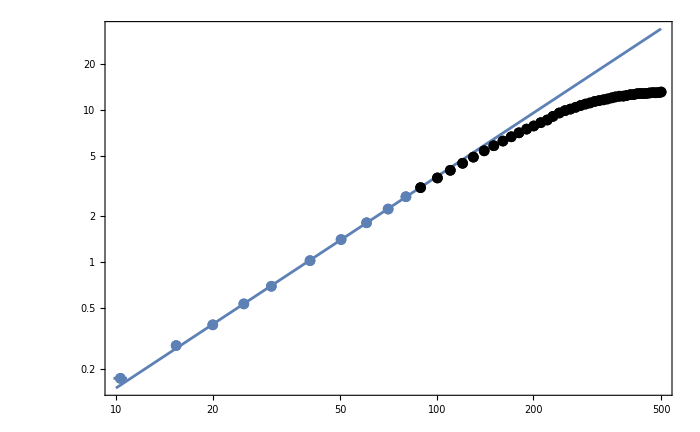

```mathematica
Show[LogLogPlot[E^pars4[[1]] x^(pars4[[2]]),{x,10,500}],ListLogLogPlot[Table[{{Around[cutData75⟦i,1⟧,cutxError75[[i]]],Around[cutData75⟦i,2⟧,cutyError75⟦i⟧]}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],pltsettings]
```

### Abb 9

```mathematica
Temp[Uh_]:=1616+97 Uh
```

```mathematica
rawDataTemp=Import[NotebookDirectory[]<>"Temperaturabhangigkeit.xlsx"][[1]];
```

```mathematica
dataTemp={#[[1]],#[[2]]*10^(-3)}&/@rawDataTemp[[All,1;;2]]
```

{{5.0047,0.0002227},{5.1022,0.0002896},{5.2041,0.0003501},{5.3012,0.0004115},{5.4002,0.0004892},{5.4923,0.000574},{5.6031,0.0007224},{5.7004,0.0008576},{5.8051,0.0010471},{5.9057,0.0012392},{6.0172,0.0015024},{6.1038,0.0017461},{6.2007,0.0020452},{6.3025,0.0024321},{6.4026,0.0028259},{6.5021,0.0032513},{6.6001,0.0037672},{6.7067,0.004382},{6.8021,0.0050954},{6.9001,0.0058175},{7.003,0.0067463}}

```mathematica
ydataTemp=#[[2]]/Temp[#[[1]]]^2&/@dataTemp;
```

```mathematica
logydataTemp=Log[ydataTemp];
```

```mathematica
xdataTemp=1/(Temp/@dataTemp[[All,1]]);
```

```mathematica
fit=LinearModelFit[Transpose[{xdataTemp, logydataTemp}],x,x]
```

FittedModel[…]

```mathematica
fit["ParameterTableEntries"]
```

{{14.3568,0.294706,48.7157,2.03219×10^-21},{-79816.5,647.151,-123.335,4.67147×10^-29}}

```mathematica
-79816.51470891564*1.38*10^(-23)
```

-1.10147×10^-18

```mathematica
(1.1014679029830358*^-18)/(1.6*10^(-19))
```

6.88417

```mathematica
LinearModelFit[Transpose[{xdataTemp,Log@ydataTemp}],x,x]
```

FittedModel[…]

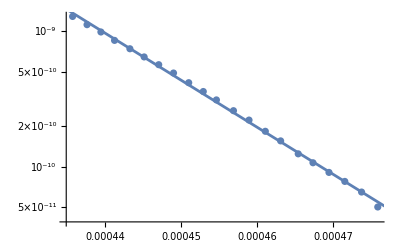

```mathematica
Show[ListLogPlot[Transpose[{xdataTemp,ydataTemp}]],LogPlot[Exp[fit[x]],{x,0,1}]]
```